```mathematica
(*Getting the partner potential*)
g=1.5;
κ=1;

(*This is the ground state wavefunction for the meson fluctuations around the steady state soliton,found by solving the linearized Schrodinger equation*)
ϕ0=Get["/home/zz3250/Wolfram Mathematica/BoundStateProfile"];
ϕ0=Interpolation[ϕ0,InterpolationOrder->10];

firstderiv[x_]:=Evaluate[D[ϕ0[a],a]/. {a->x}];
w[x_]:=-firstderiv[x]/ϕ0[x];
dw[x_]:=Evaluate[D[w[a],a]/. {a->x}];

partnerpotential[x_?NumericQ]:=w[x]^2+dw[x]+1.7925808114^2-8.5239;
```

{0.00105508,0.00108378,0.00393253,0.00404713,0.00872889,0.00898605,0.0154451,0.0159005,0.0240822,0.0247906}

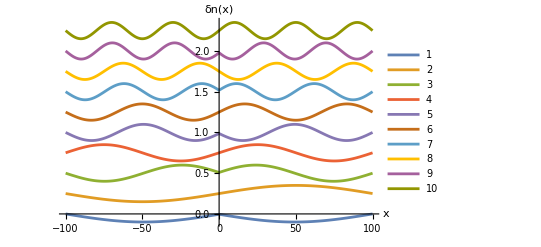

```mathematica
(*Cute Plot of the first ten eigenfunctions*)
total=10;
H2=-u''[x]+Evaluate[partnerpotential[x]]*u[x];
(*{vals,fns}=NDEigensystem[H2,u[x],{x,-100,100},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->.0625}}}];*)
{vals,fns}=NDEigensystem[{H2,DirichletCondition[u[x]==0,True]},u[x],{x,-100,100},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->.0625}}}];
Print[vals]
shift={0,1,2,3,4,5,6,7,8,9};
Plot[Evaluate[fns+shift*.25],{x,-100,100},PlotLegends->{"1","2","3","4","5","6","7","8","9","10"},AxesLabel->{"x","δn(x)"}]
```

```mathematica
(*We want to solve the eigenproblem Hψ = ω^2ψ for ψ and ω.  The Hamiltonian H=-d^2/dx^2+V2[x]*)
total=400;
H2=-u''[x]+Evaluate[partnerpotential[x]]*u[x];
{vals,fns}=NDEigensystem[{H2,DirichletCondition[u[x]==0,True]},u[x],{x,-100,100},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->.0625}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

```mathematica
(*Now let's define an ON basis of the wavefunctions.  First we check to show they are orthogonal and normalized*)
orthcheck=NIntegrate[fns[[10]]*fns[[10]],{x,-100,100}];
Print["Integral of eigenfunctions are ",orthcheck]
```

Integral of eigenfunctions are 1.

```mathematica
(*Now we want to check the overlap with an initial state of a gaussian*)
ampeven=List[];
evennums=List[];
ampodd=List[];
oddnums=List[];
δ0[x_]=Exp[-x^2];
For[i=1,i<total,i=i+2,
ampn=NIntegrate[δ0[x]*fns[[i]],{x,-100,100}];
AppendTo[ampodd,ampn];
AppendTo[oddnums,i];
];
For[i=2,i<total,i=i+2,
ampn=NIntegrate[δ0[x]*fns[[i]],{x,-100,100}];
AppendTo[ampeven,ampn];
AppendTo[evennums,i];
];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.393733}. NIntegrate obtained 0.105609 and 1.08328×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.393733}. NIntegrate obtained -0.102933 and 1.08555×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.393733}. NIntegrate obtained 0.100275 and 1.08577×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained 1.1124×10^-6 and 1.17711×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained 2.23798×10^-6 and 2.35429×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained 3.36571×10^-6 and 3.53159×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

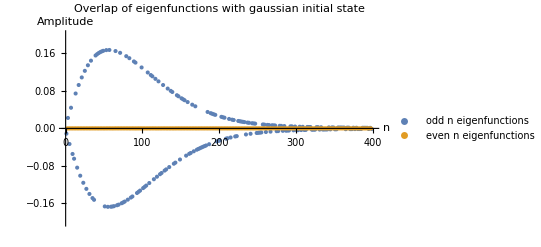

```mathematica
ListPlot[{Transpose[{oddnums,ampodd}],Transpose[{evennums,ampeven}]},PlotRange->{{0,total},{-.2,.2}},AxesLabel->{"n","Amplitude"},PlotLabel->"Overlap of eigenfunctions with gaussian initial state",PlotLegends->{"odd n eigenfunctions","even n eigenfunctions"}]
```

General::munfl: Exp[-9999.18] is too small to represent as a normalized machine number; precision may be lost.

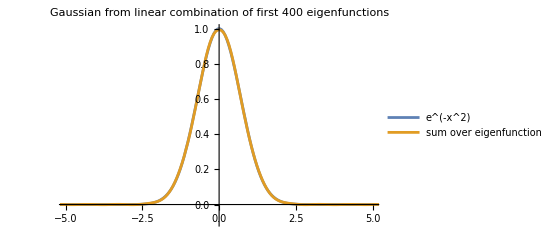

```mathematica
gaussiansum[x_]:=Sum[fns[[oddnums[[i]]]]*ampodd[[i]],{i,1,200}]
Plot[{Exp[-(x+0)^2],Evaluate[gaussiansum[x]]},{x,-100,100},PlotRange->{{-5,5},{-.1,1}},PlotLegends->{"e^(-x^2)","sum over eigenfunctions"},PlotLabel->"Gaussian from linear combination of first 400 eigenfunctions"]
```

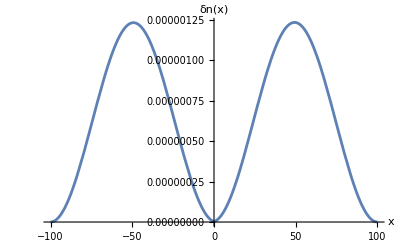

```mathematica
(*Time Evolution of each mode*)
equation=D[ψ[x,t],{t,2}]+(partnerpotential[x+10])*ψ[x,t]==D[ψ[x,t],{x,2}];
ψ0[x_]:=fns[[oddnums[[1]]]]*ampodd[[1]];
Plot[Evaluate[Abs[ψ0[x]^2]],{x,-100,100},AxesLabel->{"x","δn(x)"}]
```

```mathematica
tdsol=NDSolve[{equation,ψ[x,0]==ψ0[x],(D[ψ[x,t],t]/. t->0)==I*vals[[1]]*ψ0[x],ψ[-100,t]==0,ψ[100,t]==0},ψ,{x,-100,100},{t,0,20}]
```

{{ψ→InterpolatingFunction[…]}}

```mathematica
animation=Animate[Plot[Evaluate[Abs[ψ[x,t]/. tdsol]^2],{x,-100,100},PlotRange->{{-100,100},{0,.000002}},AxesLabel->{"x","|ψ[x]|^2"},PerformanceGoal->"Quality"],{t,0,20}]
```

```mathematica
(*Time evolution of 2 modes :)*)
equation=D[ψ[x,t],{t,2}]+(partnerpotential[x+10])*ψ[x,t]==D[ψ[x,t],{x,2}];
wavefunctions=List[];
ψ0[x_]:=fns[[oddnums[[1]]]]*ampodd[[1]];
tdsol=NDSolve[{equation,ψ[x,0]==ψ0[x],(D[ψ[x,t],t]/. t->0)==I*vals[[1]]*ψ0[x],ψ[-100,t]==0,ψ[100,t]==0},ψ,{x,-100,100},{t,0,20}];
func[x_,t_]:=ψ[x,t]/. tdsol;
AppendTo[wavefunctions,func[x,t][[1]]];

ψ0[x_]:=fns[[oddnums[[2]]]]*ampodd[[2]];
tdsol=NDSolve[{equation,ψ[x,0]==ψ0[x],(D[ψ[x,t],t]/. t->0)==I*vals[[2]]*ψ0[x],ψ[-100,t]==0,ψ[100,t]==0},ψ,{x,-100,100},{t,0,20}];
func[x_,t_]:=ψ[x,t]/. tdsol;
AppendTo[wavefunctions,func[x,t][[1]]];
```

```mathematica
animation=Animate[Plot[Evaluate[Abs[wavefunctions[[2]]/. t->t0]^2],{x,-100,100},PlotRange->{{-100,100},{0,.000005}},AxesLabel->{"x","|ψ[x]|^2"},PerformanceGoal->"Quality"],{t0,0,20}]
```

```mathematica
wavefunctionssum[x_,t0_]:=Sum[wavefunctions[[i]]/. t->t0,{i,1,2}];
Print[wavefunctionssum[x,t0]]

animation=Animate[Plot[Evaluate[Abs[wavefunctionssum[x,t0]]^2],{x,-100,100},PlotRange->{{-100,100},{0,.00001}},AxesLabel->{"x","|ψ[x]|^2"},PerformanceGoal->"Quality"],{t0,0,20}]
```

InterpolatingFunction[…][x,t0]+InterpolatingFunction[…][x,t0]

```mathematica
(*all modes*)
(*Define the equation*)equation=D[ψ[x,t],{t,2}]+(partnerpotential[x+10])*ψ[x,t]==D[ψ[x,t],{x,2}];

(*Initialize the wavefunctions list*)
wavefunctions={};

(*Populate the wavefunctions list*)
For[i=1,i<=25,i++,
ψ0[x_]:=fns[[oddnums[[i]]]]*ampodd[[i]];
tdsol=NDSolve[{equation,ψ[x,0]==ψ0[x],(D[ψ[x,t],t]/. t->0)==I*vals[[i]]*ψ0[x],ψ[-100,t]==0,ψ[100,t]==0},ψ,{x,-100,100},{t,0,20}];
func[x_,t_]:=ψ[x,t]/. tdsol;
AppendTo[wavefunctions,func[x,t]];
];

(*Define the wavefunction sum*)
wavefunctionssum[x_,t0_]:=Evaluate[Sum[wavefunctions[[i]],{i,1,Length[wavefunctions]}]]/. t->t0;
```

Part::partd: Part specification oddnums⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression oddnums⟦1⟧ cannot be used as a part specification.

Part::partd: Part specification ampodd⟦1⟧ is longer than depth of object.

Part::partd: Part specification vals⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression oddnums⟦1⟧ cannot be used as a part specification.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{partnerpotential[Plus[«2»]] ψ[x,t]+ψ^(0,2)[x,t]==ψ^(2,0)[x,t],ψ[x,0]==ampodd⟦1⟧ fns⟦oddnums⟦1⟧⟧,ψ^(0,1)[x,0]==ⅈ ampodd⟦1⟧ fns⟦oddnums⟦1⟧⟧ vals⟦1⟧,ψ[-100,t]==0,ψ[100,t]==0},ψ,{x,-100,100},{t,0,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::pkspec1: The expression oddnums⟦2⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
(*Create the animation*)
animation=Animate[Plot[Evaluate[Abs[wavefunctionssum[x,t0]]^2],{x,-100,100},PlotRange->{{-100,100},{0,1}},AxesLabel->{"x","|ψ[x]|^2"},PerformanceGoal->"Quality"],{t0,0,20}]
```